## Partials 1-16 and the viola strings tuned normally

◀     |     ▶

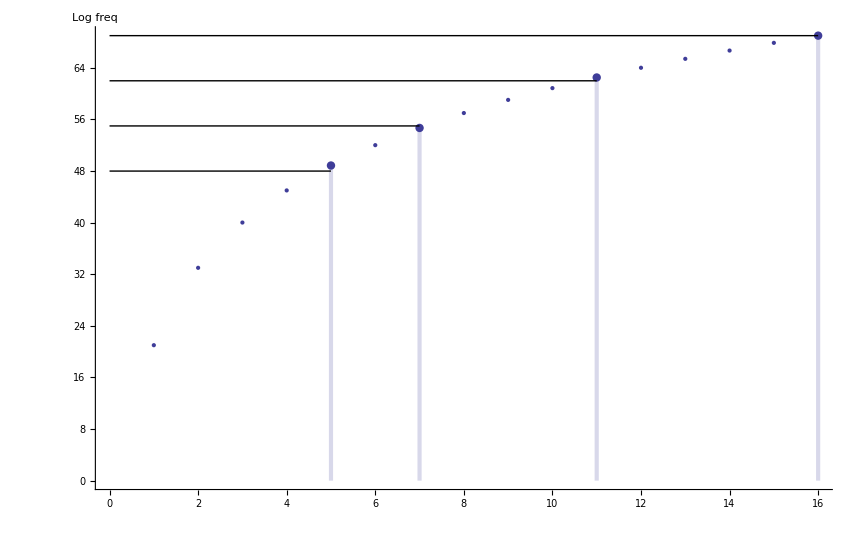

```mathematica
Module[{hs=harmonicSeries[27.5,16],hsl,st},
hsl=ftom[hs];
st={5,7,11,16};
Show[
ListPlot[hsl,AxesLabel->{"","Log freq"}],
ListPlot[Partition[Riffle[st,ftom[st*27.5]],2],Filling->Axis,PlotStyle->AbsolutePointSize[6.03],FillingStyle->Directive[AbsoluteThickness[2.99],Hue[0.67, 0.6, 0.6], Opacity[0.2]],AxesOrigin->{0,0}],

Graphics[{Line[{{0.,48},{5,48}}],Line[{{0.,55},{7,55}}],Line[{{0.,62},{11,62}}],Line[{{0.,69},{16,69}}]}]
]
]
```

## Natural harmonics on the retuned viola

◀     |     ▶

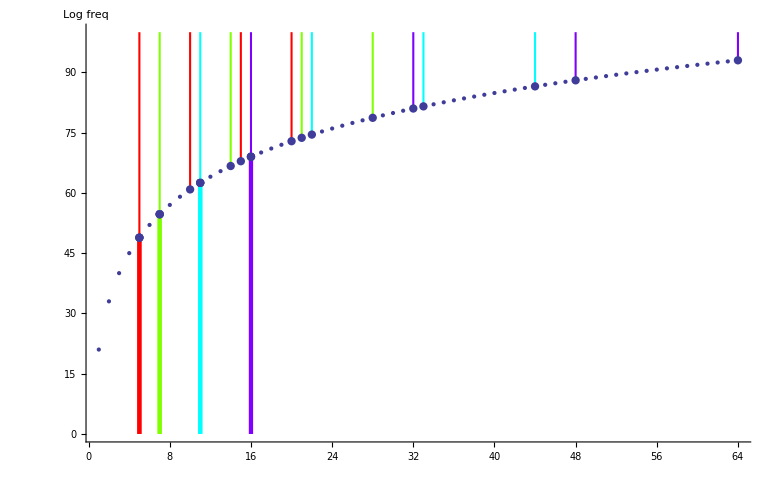

```mathematica
Module[{hs=harmonicSeries[27.5,64],hsl,st},
hsl=ftom[hs];
st={5,7,11,16};
Show[
ListPlot[hsl,AxesLabel->{"","Log freq"}],
(*ListPlot[Partition[Riffle[st,ftom[st*27.5]],2],Filling->Axis,PlotStyle->AbsolutePointSize[6],FillingStyle->Directive[AbsoluteThickness[3],Hue[0.67, 0.6, 0.6], Opacity[0.2]],AxesOrigin->{0,0}],*)
ListPlot[{{5,ftom[5*27.5]}},Filling->Axis,PlotStyle->AbsolutePointSize[6],FillingStyle->Directive[AbsoluteThickness[3],Hue[0,1,1], Opacity[1]],AxesOrigin->{0,0}],

ListPlot[{{7,ftom[7*27.5]}},Filling->Axis,PlotStyle->AbsolutePointSize[6],FillingStyle->Directive[AbsoluteThickness[3],Hue[0.25,1,1], Opacity[1]],AxesOrigin->{0,0}],

ListPlot[{{11,ftom[11*27.5]}},Filling->Axis,PlotStyle->AbsolutePointSize[6],FillingStyle->Directive[AbsoluteThickness[3],Hue[0.5,1,1], Opacity[1]],AxesOrigin->{0,0}],

ListPlot[{{16,ftom[16*27.5]}},Filling->Axis,PlotStyle->AbsolutePointSize[6],FillingStyle->Directive[AbsoluteThickness[3],Hue[0.75,1,1], Opacity[1]],AxesOrigin->{0,0}],

ListPlot[Partition[Riffle[Range[4]*5,ftom[Range[4]*5*27.5]],2],Filling->Top,PlotStyle->AbsolutePointSize[6],FillingStyle->Directive[AbsoluteThickness[1.5],Hue[0, 1, 1], Opacity[1]],AxesOrigin->{0,0},PlotRange->{0,100}],

ListPlot[Partition[Riffle[Range[4]*7,ftom[Range[4]*7*27.5]],2],Filling->Top,PlotStyle->AbsolutePointSize[6],FillingStyle->Directive[AbsoluteThickness[1.5],Hue[0.25,1,1], Opacity[1]],AxesOrigin->{0,0},PlotRange->{0,100}],

ListPlot[Partition[Riffle[Range[4]*11,ftom[Range[4]*11*27.5]],2],Filling->Top,PlotStyle->AbsolutePointSize[6],FillingStyle->Directive[AbsoluteThickness[1.5],Hue[0.5, 1,1], Opacity[1]],AxesOrigin->{0,0},PlotRange->{0,100}],

ListPlot[Partition[Riffle[Range[4]*16,ftom[Range[4]*16*27.5]],2],Filling->Top,PlotStyle->AbsolutePointSize[6],FillingStyle->Directive[AbsoluteThickness[1.5],Hue[0.75,1,1], Opacity[1]],AxesOrigin->{0,0},PlotRange->{0,100}]

(*Graphics[{Line[{{0.,48},{5,48}}],Line[{{0.,55},{7,55}}],Line[{{0.,62},{11,62}}],Line[{{0.,69},{16,69}}]}]*)
]
]
```

## Harmonic series

◀     |     ▶

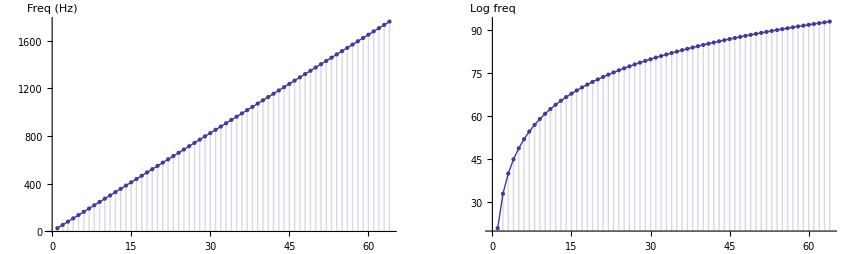

```mathematica
Module[{h=harmonicSeries[27.5,64]},plotLinLogArray[h]]
```

## Hailstone sequence starting at 880

◀     |     ▶

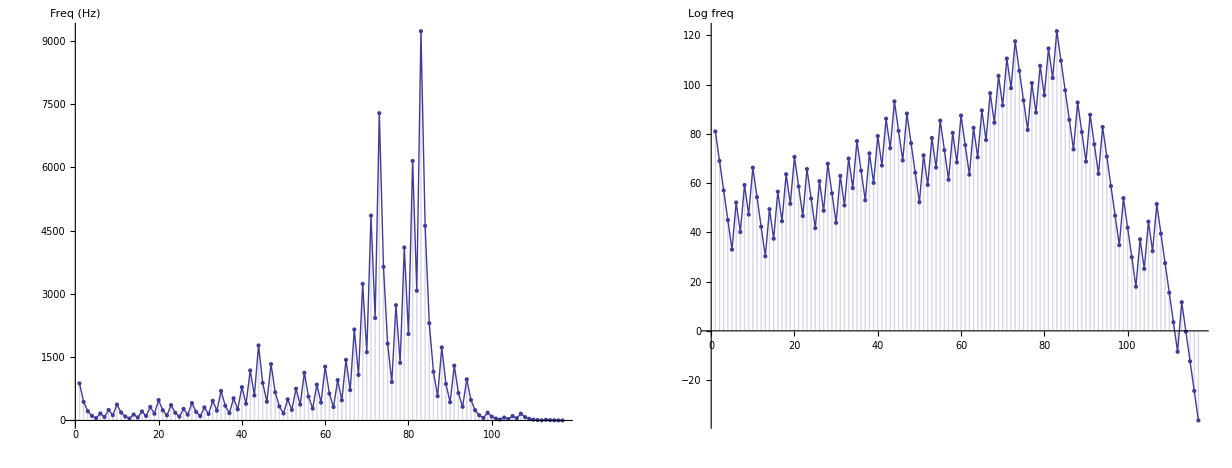

```mathematica
Module[{h=hailstone[880]},plotLinLogArray[h]]
```

## Sorted hailstone sequence starting at 880

◀     |     ▶

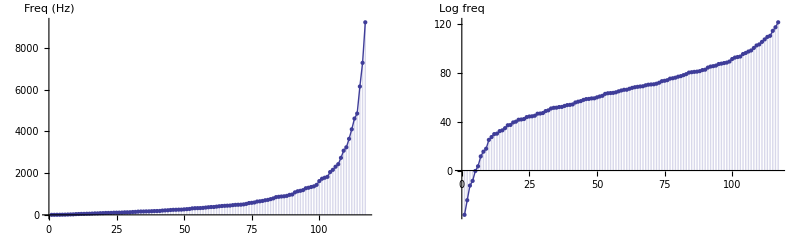

```mathematica
Module[{h=Sort[hailstone[880]]},plotLinLogArray[h]]
```

## Beta Distribution

◀     |     ▶

```mathematica
Manipulate[Plot[PDF[BetaDistribution[a, b],x],{x,0.,1.}],{{a,2.},1.,10.},{{b,2.},1.,10.}]
```

```mathematica
hailstone[x_]:=NestWhileList[Piecewise[{{#/2, Mod[#,2]==0}, {#*3+1, Mod[#,2]==1}}]&,x,#>1&]
```

```mathematica
harmonicSeries[x_,n_]:=NestList[#+x&,x,n-1]
```

```mathematica
ftom[f_]:=Log[2^(1/12),f/27.5]+21
```

```mathematica
mtof[m_]:=27.5*(2^(1/12))^(m-21)
```

```mathematica
plotLinLogArray[l_]:=Show[GraphicsArray[{Show[ListPlot[l,PlotRange->Full,Filling->Axis,AxesLabel->{"","Freq (Hz)"}],ListLinePlot[l,PlotRange->Full]],Show[ListPlot[ftom[l],PlotRange->Full,Filling->Axis,AxesLabel->{"","Log freq"}],ListLinePlot[ftom[l],PlotRange->Full]]}]]
```

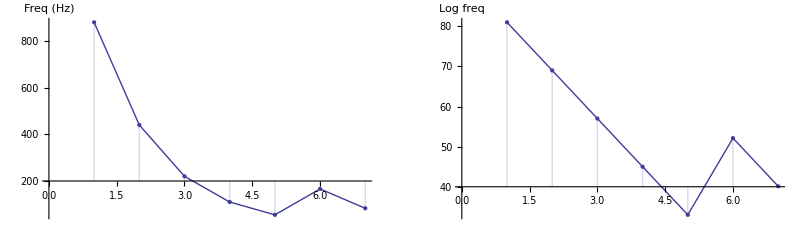

```mathematica
plotLinLogArray[{880,440,220,110,55,166,83}]
```